При однократной дозе препарата в желудочно-кишечный тракт больше ничего не поступает, поэтому выходной член для желудочно-кишечного тракта только один, препарат (х0) растворяется в желудочно-кишечном тракте (с разной скоростью растворения k1 для каждого препарата) и диффундирует в кровь.
dx/dt=-k1 x , x(0)=x0;

х - количество препарата в желудочно-кишечном тракте как функция времени t, найти точное решение уравнения. На примере лекарства от простуды (два ингредиента в препарате:k1=1,386/0,6931) нарисуйте кривую изменения количества лекарства в желудочно-кишечном тракте во времени.

```mathematica
ClearAll[k1,x0];
func1=DSolveValue[{x'[t]==-k1*x[t],x[0]==x0},x[t],t]
```

ⅇ^(-k1 t) x0

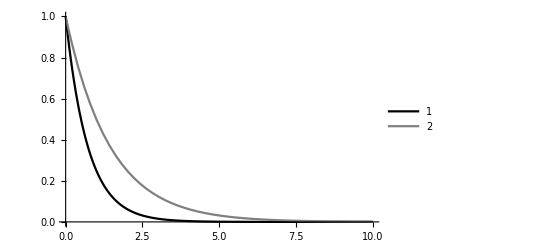

```mathematica
x0=1;
Plot[{func1/. k1->1.386,func1/. k1->0.6931},{t,0,10},PlotLegends->{"1","2"},PlotRange->{Automatic,{0,1}},PlotStyle->{Black,Gray}]
```

В крови исходное количество препарата равно нулю (y0=0), увеличивается по мере растворения препарата в желудочно-кишечном тракте (k1 x) и уменьшается по мере его выведения из организма (-k2 y).
dy/dt=k1 x-k2 y , y(0)=y0;

y - количество препарата в крови как функция времени t.Используйте точное решение, найденное в первом уравнении, чтобы получить точное решение этого уравнения, и постройте график изменения количества лекарства в крови.

```mathematica
ClearAll[k1,k2,x0];
func2=DSolveValue[{y'[t]==k1*x0*Exp[-k1*t]-k2*y[t],y[0]==0},y[t],t]
```

(ⅇ^(-k2 t) (-1+ⅇ^((-k1+k2) t)) k1 x0)/(-k1+k2)

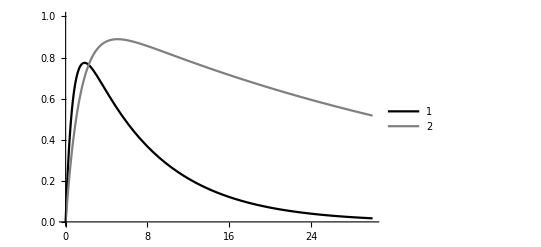

```mathematica
x0=1;
Plot[{func2/. {k1->1.386,k2->0.1386},func2/.{ k1->0.6931,k2->0.0231}},{t,0,30},PlotLegends->{"1","2"},PlotRange->{Automatic,{0,1}},PlotStyle->{Black,Gray}]
```

По мере увеличения t и x, и y приближаются к нулю, и скорость, с которой это происходит, варьируется в зависимости от коэффициентов k1 и k2, связанных с каждым препаратом.

```mathematica
ClearAll[k1,k2];
Manipulate[func=NDSolveValue[{x'[t]==-k1*x[t],y'[t]==k1*x[t]-k2*y[t],x[0]==1,y[0]==0},{x,y},{t,0,10}];
Grid[{{Plot[func[[1]][t],{t,0,10},PlotLegends->{"ЖКТ"},PlotRange->{Automatic,{0,1}}],Plot[func[[2]][t],{t,0,10},PlotLegends->{"Кровь"},PlotRange->{Automatic,{0,1}}]}}],{{k1,1.386,"k1"},0.1,3,0.01},{{k2,0.1386,"k2"},0.01,1,0.001}]
```

По мере того, как мы продолжаем принимать препарат, препарат продолжает поступать в желудочно-кишечный тракт (I – количество препарата, принятое в единицу времени), и уравнение соответственно меняется.
dx/dt=I-k1 x,x(0)=0;

Получите точное решение и по очереди нарисуйте кривую изменения.

```mathematica
ClearAll[k1,II];
funcc1=DSolveValue[{x'[t]==II-k1*x[t],x[0]==0},x[t],t]
```

(ⅇ^(-k1 t) (-1+ⅇ^(k1 t)) II)/k1

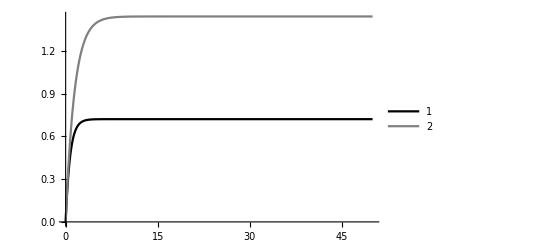

```mathematica
II=1;
Plot[{funcc1/. k1->1.386,funcc1/. k1->0.6931},{t,0,50},PlotLegends->{"1","2"},PlotRange->{Automatic,Automatic},PlotStyle->{Black,Gray}]
```

```mathematica
ClearAll[k1,k2,II];
funcc2=DSolveValue[{y'[t]==II*(1-Exp[-k1*t])-k2*y[t],y[0]==0},y[t],t]
```

-(ⅇ^(-((k1-k2) t)-k2 t) II (-ⅇ^(k1 t) k1+ⅇ^((k1-k2) t) k1-k2+ⅇ^(k1 t) k2))/((k1-k2) k2)

```mathematica
Simplify[funcc2]
```

(II (k1-ⅇ^(-k2 t) k1+(-1+ⅇ^(-k1 t)) k2))/((k1-k2) k2)

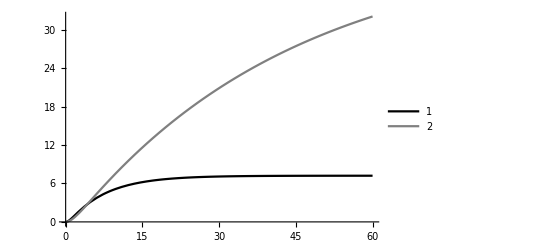

```mathematica
II=1;
Plot[{funcc2/. {k1->1.386,k2->0.1386},funcc2/.{ k1->0.6931,k2->0.0231}},{t,0,60},PlotLegends->{"1","2"},PlotRange->{Automatic,Automatic},PlotStyle->{Black,Gray}]
```

Возьмите произвольные значения k1, k2 и I, при t→∞,x→I/k1,y→ I/k2.

```mathematica
ClearAll[k1,k2];
Manipulate[
funcc=NDSolveValue[{x'[t]==II-k1*x[t],y'[t]==k1*x[t]-k2*y[t],x[0]==0,y[0]==0},{x,y},{t,0,30}];
Grid[{{Plot[funcc[[1]][t],{t,0,30},PlotLegends->{"ЖКТ"},PlotRange->{Automatic,Automatic}],Plot[funcc[[2]][t],{t,0,30},PlotLegends->{"Кровь"},PlotRange->{Automatic,Automatic}]}}],{{k1,1.386,"k1"},0.1,3,0.01},{{k2,0.1386,"k2"},0.01,1,0.001},{{II,1,"I"},0.01,10,0.001}]
```